```mathematica
a(1+a^4)ϕ''[a]+2(3a^4+2)ϕ'[a]+a(4a^2+k^2)ϕ[a]==0
DSolve[%, ϕ[a], a]
```

a (4 a^2+k^2) ϕ[a]+2 (2+3 a^4) ϕ'[a]+a (1+a^4) ϕ''[a]==0

{{ϕ[a]→(ⅇ^((-1+K[1]^4+k^2 K[1]^6+2 K[1]^8+ⅈ √(k^2 (-4+k^4)) K[1]^3 √(1+K[1]^4))/(K[1] (1+K[1]^4) (1+k^2 K[1]^2+K[1]^4))K[1]1a) C[1])/(a^2 (1+a^4)^(1/4))+(ⅇ^((-1+K[1]^4+k^2 K[1]^6+2 K[1]^8+ⅈ √(k^2 (-4+k^4)) K[1]^3 √(1+K[1]^4))/(K[1] (1+K[1]^4) (1+k^2 K[1]^2+K[1]^4))K[1]1a) C[2] ⅇ^(-2 (-1+K[1]^4+k^2 K[1]^6+2 K[1]^8+ⅈ √(k^2 (-4+k^4)) K[1]^3 √(1+K[1]^4))/(K[1] (1+K[1]^4) (1+k^2 K[1]^2+K[1]^4))K[1]1K[2])K[2]1a)/(a^2 (1+a^4)^(1/4))}}

```mathematica
ϕ[a_]:=(1+a^4)^(1/4)Exp[1/2I ArcTan[a^2]]HeunG[-1,1/4(5-K^2 I),1,5/2,5/2,1/2,a^2I]
```

```mathematica
a(1+a^4)ϕ''[a]+2(3a^4+2)ϕ'[a]+a(4a^2+K^2)ϕ[a]//FullSimplify
```

0

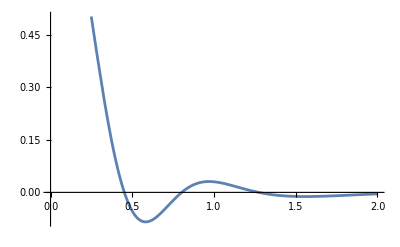

```mathematica
Plot[{ϕ[a]/.{K->10}},{a,0,2}]
```

```mathematica
a(1-a^2)^2y''[a]+2(3a^2-2)(a^2-1)y'[a]+a(4a^2+K^2)y[a]==0
DSolve[%, y[a], a]
```

a (4 a^2+K^2) y[a]+2 (-1+a^2) (-2+3 a^2) y'[a]+a (1-a^2)^2 y''[a]==0

{{y[a]→((1-a)^(1/2 √(-4-K^2)) (1+a)^(-1/2 √(-4-K^2)) (1+a (a+√(-4-K^2))) C[1])/a^3-((1-a)^(-1/2 √(-4-K^2)) (1+a)^(1/2 √(-4-K^2)) (1+a^2+a √(-4-K^2)) (-1+2 a^2-a^4+a^2 K^2+2 a √(-4-K^2)+2 a^3 √(-4-K^2)) C[2])/(2 a^3 √(-4-K^2) (8+K^2) (1+6 a^2+a^4+a^2 K^2))}}

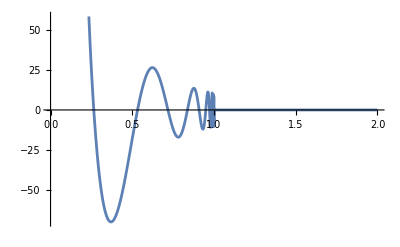

```mathematica
Plot[{Re[((1-a)^(1/2 √(-4-K^2)) (1+a)^(-1/2 √(-4-K^2)) (1+a (a+√(-4-K^2))))/a^3/.{K->10}]
},
{a,0,2}
]
```

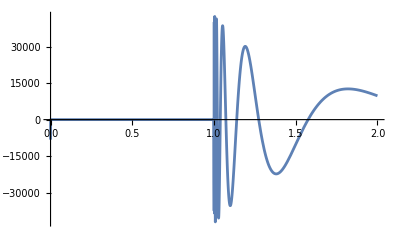

```mathematica
Plot[{Re[((1-a)^(-1/2 √(-4-K^2)) (1+a)^(1/2 √(-4-K^2)) (1+a^2+a √(-4-K^2)) (-1+2 a^2-a^4+a^2 K^2+2 a √(-4-K^2)+2 a^3 √(-4-K^2)))/(2 a^3 √(-4-K^2) (8+K^2) (1+6 a^2+a^4+a^2 K^2))/.{K->10}]
},
{a,0,2}
]
```

```mathematica
Series[((1-a)^(1/2 √(-4-K^2)) (1+a)^(-1/2 √(-4-K^2)) (1+a (a+√(-4-K^2))))/a^3,{a,0,2}]
```

1/a^3+(6+K^2)/(2 a)+1/3 (-8 √(-4-K^2)-K^2 √(-4-K^2))+1/8 (-32-12 K^2-K^4) a+1/30 (8 K^2 √(-4-K^2)+K^4 √(-4-K^2)) a^2+O[a]^3

```mathematica
Series[((1-a)^(-1/2 √(-4-K^2)) (1+a)^(1/2 √(-4-K^2)) (1+a^2+a √(-4-K^2)) (-1+2 a^2-a^4+a^2 K^2+2 a √(-4-K^2)+2 a^3 √(-4-K^2)))/(2 a^3 √(-4-K^2) (8+K^2) (1+6 a^2+a^4+a^2 K^2)),{a,0,2}]
```

-1/(2 (√(-4-K^2) (8+K^2)) a^3)+(-6-K^2)/(4 √(-4-K^2) (8+K^2) a)-1/6+((4+K^2) a)/(16 √(-4-K^2))+(K^2 a^2)/60+O[a]^3

```mathematica
Series[3I(1/(2 Sqrt[4+K^2](8+K^2))((1-a)^(1/2 √(-4-K^2)) (1+a)^(-1/2 √(-4-K^2)) (1+a (a+√(-4-K^2))))/a^3+I((1-a)^(-1/2 √(-4-K^2)) (1+a)^(1/2 √(-4-K^2)) (1+a^2+a √(-4-K^2)) (-1+2 a^2-a^4+a^2 K^2+2 a √(-4-K^2)+2 a^3 √(-4-K^2)))/(2 a^3 √(-4-K^2) (8+K^2) (1+6 a^2+a^4+a^2 K^2))),{a,0,1}]/.{K->1}//FullSimplify
```

1+O[a]^2

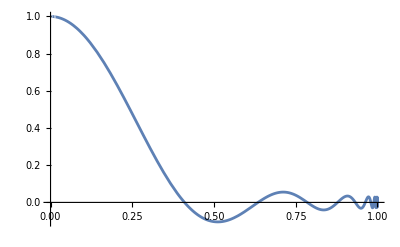

```mathematica
Plot[{3I(1/(2 Sqrt[4+K^2](8+K^2))((1-a)^(1/2 √(-4-K^2)) (1+a)^(-1/2 √(-4-K^2)) (1+a (a+√(-4-K^2))))/a^3+I((1-a)^(-1/2 √(-4-K^2)) (1+a)^(1/2 √(-4-K^2)) (1+a^2+a √(-4-K^2)) (-1+2 a^2-a^4+a^2 K^2+2 a √(-4-K^2)+2 a^3 √(-4-K^2)))/(2 a^3 √(-4-K^2) (8+K^2) (1+6 a^2+a^4+a^2 K^2)))/.{K->10}
},
{a,0,1}
]
```

```mathematica
a(1+a^2)^2y''[a]+2(3a^2+2)(a^2+1)y'[a]+a(4a^2+K^2)y[a]==0
DSolve[%, y[a], a]
```

a (4 a^2+K^2) y[a]+2 (1+a^2) (2+3 a^2) y'[a]+a (1+a^2)^2 y''[a]==0

{{y[a]→(ⅇ^(ⅈ √(-4+K^2) ArcTan[a]) (-1+a^2+ⅈ a √(-4+K^2)) C[1])/a^3+(ⅇ^(-ⅈ √(-4+K^2) ArcTan[a]) (-1+a^2+ⅈ a √(-4+K^2)) (ⅈ+2 ⅈ a^2+ⅈ a^4-ⅈ a^2 K^2-2 a √(-4+K^2)+2 a^3 √(-4+K^2)) C[2])/(2 a^3 (-8+K^2) √(-4+K^2) (1-6 a^2+a^4+a^2 K^2))}}

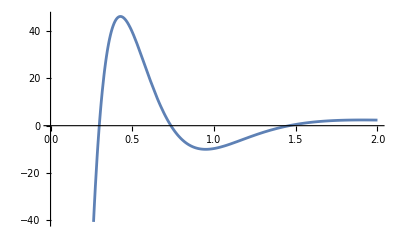

```mathematica
Plot[{Re[(ⅇ^(ⅈ √(-4+K^2) ArcTan[a]) (-1+a^2+ⅈ a √(-4+K^2)))/a^3/.{K->10}]
},
{a,0,2}
]
```

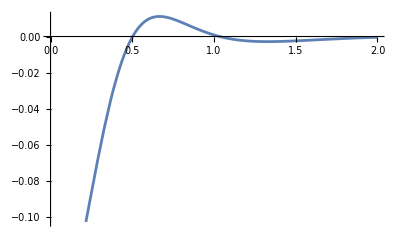

```mathematica
Plot[{Re[(ⅇ^(-ⅈ √(-4+K^2) ArcTan[a]) (-1+a^2+ⅈ a √(-4+K^2)) (ⅈ+2 ⅈ a^2+ⅈ a^4-ⅈ a^2 K^2-2 a √(-4+K^2)+2 a^3 √(-4+K^2)))/(2 a^3 (-8+K^2) √(-4+K^2) (1-6 a^2+a^4+a^2 K^2))/.{K->10}]
},
{a,0,2}
]
```

```mathematica
Series[(ⅇ^(ⅈ √(-4+K^2) ArcTan[a]) (-1+a^2+ⅈ a √(-4+K^2)))/a^3,{a,0,2}]
```

-1/a^3+(6-K^2)/(2 a)-1/3 ⅈ (-8+K^2) √(-4+K^2)+1/8 (32-12 K^2+K^4) a+1/30 ⅈ √(-4+K^2) (-8 K^2+K^4) a^2+O[a]^3

```mathematica
Series[(ⅇ^(-ⅈ √(-4+K^2) ArcTan[a]) (-1+a^2+ⅈ a √(-4+K^2)) (ⅈ+2 ⅈ a^2+ⅈ a^4-ⅈ a^2 K^2-2 a √(-4+K^2)+2 a^3 √(-4+K^2)))/(2 a^3 (-8+K^2) √(-4+K^2) (1-6 a^2+a^4+a^2 K^2)),{a,0,2}]
```

-ⅈ/(2 (-8+K^2) √(-4+K^2) a^3)-(ⅈ (-6+K^2))/(4 (-8+K^2) √(-4+K^2) a)-1/6+1/16 ⅈ √(-4+K^2) a+(K^2 a^2)/60+O[a]^3

```mathematica
Series[3I(1/(2 Sqrt[K^2-4](K^2-8))(ⅇ^(ⅈ √(-4+K^2) ArcTan[a]) (-1+a^2+ⅈ a √(-4+K^2)))/a^3+I(ⅇ^(-ⅈ √(-4+K^2) ArcTan[a]) (-1+a^2+ⅈ a √(-4+K^2)) (ⅈ+2 ⅈ a^2+ⅈ a^4-ⅈ a^2 K^2-2 a √(-4+K^2)+2 a^3 √(-4+K^2)))/(2 a^3 (-8+K^2) √(-4+K^2) (1-6 a^2+a^4+a^2 K^2))),{a,0,1}]/.{K->10}//FullSimplify
```

1+O[a]^2

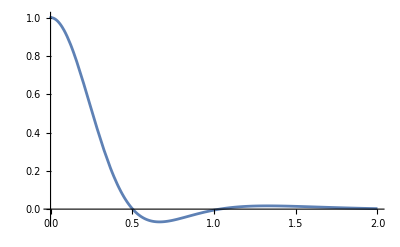

```mathematica
Plot[{3I(1/(2 Sqrt[K^2-4](K^2-8))(ⅇ^(ⅈ √(-4+K^2) ArcTan[a]) (-1+a^2+ⅈ a √(-4+K^2)))/a^3+I(ⅇ^(-ⅈ √(-4+K^2) ArcTan[a]) (-1+a^2+ⅈ a √(-4+K^2)) (ⅈ+2 ⅈ a^2+ⅈ a^4-ⅈ a^2 K^2-2 a √(-4+K^2)+2 a^3 √(-4+K^2)))/(2 a^3 (-8+K^2) √(-4+K^2) (1-6 a^2+a^4+a^2 K^2)))/.{K->10}
},
{a,0,2},PlotRange-> All
]
```